```mathematica
SetDirectory[NotebookDirectory[]];
dat=Import["RC.TXT"];
```

```mathematica
headerList={"Pascals(in/Hg)","Altitude(ft)","Temperature(*C)","Time(s)"};
```

```mathematica
(* Split file by tabs *)
datList=StringSplit[dat,"\t"];
datList//Short;
```

```mathematica
(* Split file by newlines *)
nDatList=StringSplit[#,"\n"]&/@datList;
```

```mathematica
test=nDatList[[2]];
test
```

{Pascals(in/Hg),Altitude(ft),Temperature(*C),Time(s),28.33,1577.47,23.94,0,28.33,1578.29,23.94,1,28.33,1577.88,24.00,2,28.33,1576.86,24.00,3,28.33,1577.68,24.00,4,28.33,1578.70,23.94,5,28.33,1579.12,23.94,5,28.33,1579.93,23.94,6,28.33,1579.52,23.94,7,28.33,1577.68,24.00,8,28.33,1578.91,24.00,9,28.33,1578.70,24.00,9,28.33,1578.29,24.00,10,28.33,1577.88,24.00,11,28.33,1579.52,23.94,12,28.33,1576.86,24.00,13,28.33,1577.88,24.00,14,28.33,1576.45,24.00,14,28.33,1576.45,24.00,15}

```mathematica
test=StringSplit[#,","]&/@test;
test
```

{{Pascals(in/Hg),Altitude(ft),Temperature(*C),Time(s)},{28.33,1577.47,23.94,0},{28.33,1578.29,23.94,1},{28.33,1577.88,24.00,2},{28.33,1576.86,24.00,3},{28.33,1577.68,24.00,4},{28.33,1578.70,23.94,5},{28.33,1579.12,23.94,5},{28.33,1579.93,23.94,6},{28.33,1579.52,23.94,7},{28.33,1577.68,24.00,8},{28.33,1578.91,24.00,9},{28.33,1578.70,24.00,9},{28.33,1578.29,24.00,10},{28.33,1577.88,24.00,11},{28.33,1579.52,23.94,12},{28.33,1576.86,24.00,13},{28.33,1577.88,24.00,14},{28.33,1576.45,24.00,14},{28.33,1576.45,24.00,15}}

```mathematica
test = Drop[test,1];
test
```

{{28.33,1577.47,23.94,0},{28.33,1578.29,23.94,1},{28.33,1577.88,24.00,2},{28.33,1576.86,24.00,3},{28.33,1577.68,24.00,4},{28.33,1578.70,23.94,5},{28.33,1579.12,23.94,5},{28.33,1579.93,23.94,6},{28.33,1579.52,23.94,7},{28.33,1577.68,24.00,8},{28.33,1578.91,24.00,9},{28.33,1578.70,24.00,9},{28.33,1578.29,24.00,10},{28.33,1577.88,24.00,11},{28.33,1579.52,23.94,12},{28.33,1576.86,24.00,13},{28.33,1577.88,24.00,14},{28.33,1576.45,24.00,14},{28.33,1576.45,24.00,15}}

```mathematica
test=ToExpression/@test;
test
```

{{28.33,1577.47,23.94,0},{28.33,1578.29,23.94,1},{28.33,1577.88,24.,2},{28.33,1576.86,24.,3},{28.33,1577.68,24.,4},{28.33,1578.7,23.94,5},{28.33,1579.12,23.94,5},{28.33,1579.93,23.94,6},{28.33,1579.52,23.94,7},{28.33,1577.68,24.,8},{28.33,1578.91,24.,9},{28.33,1578.7,24.,9},{28.33,1578.29,24.,10},{28.33,1577.88,24.,11},{28.33,1579.52,23.94,12},{28.33,1576.86,24.,13},{28.33,1577.88,24.,14},{28.33,1576.45,24.,14},{28.33,1576.45,24.,15}}

```mathematica
test=PrependTo[test,headerList];
test
```

{{Pascals(in/Hg),Altitude(ft),Temperature(*C),Time(s)},{28.33,1577.47,23.94,0},{28.33,1578.29,23.94,1},{28.33,1577.88,24.,2},{28.33,1576.86,24.,3},{28.33,1577.68,24.,4},{28.33,1578.7,23.94,5},{28.33,1579.12,23.94,5},{28.33,1579.93,23.94,6},{28.33,1579.52,23.94,7},{28.33,1577.68,24.,8},{28.33,1578.91,24.,9},{28.33,1578.7,24.,9},{28.33,1578.29,24.,10},{28.33,1577.88,24.,11},{28.33,1579.52,23.94,12},{28.33,1576.86,24.,13},{28.33,1577.88,24.,14},{28.33,1576.45,24.,14},{28.33,1576.45,24.,15}}

```mathematica
test=Dataset[Map[AssociationThread[First[test],#]&,Rest[test]]];
test
```

Dataset[<>]

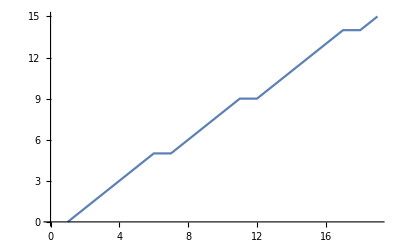

```mathematica
ListLinePlot[test[[All,4]]]
```

```mathematica
(*headerString="Pascals--Inches (Hg)--,Altitude--meters--,Temperature--*C--,Millis()";
cleanHeaderString = "Pascals(in/Hg),Altitude(m),Temperature(*C),Time(s)";*)
```

```mathematica
(*fDatThreadList=Dataset[Map[AssociationThread[First[fDatList],#]&,Rest[fDatList]]]*)
```